## Some random reverse engineering attempts

(SSS code not needed for this material, only local commands/functions used, can be run in WolframCloud.)

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["SSS`"];
```

### Code

```mathematica
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
```

```mathematica
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
(*
,
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
*)
}];
(* 1st line looks for a repeated set (2 to ∞ reps) of (0 or more) integers, 2nd line looks for a repeated subsequence (2 to ∞ reps) of at least 2 sets of integers,
3rd line applies to all left over sets. *)

FromReducedNetDifferenceSets[ll_List]:=Flatten[ll /.(n_)·l_List :>Sequence@@Table[l,{n}],1]
```

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs, paddedlist,gatheredlist,lasteltslist},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;  (* this creates a pair of integers from each link in the network:  {starting node, link length} *)
paddedlist = Join[{#,0}& /@ Range[Max[First/@nodediffpairs]],nodediffpairs];
gatheredlist=Gather[paddedlist,First[#1]==First[#2]&];
lasteltslist=Map[Last, gatheredlist,{2}];
If[$debug, 
Print["net: ", net]; 
Print["list of {node, link_length} pairs: ", nodediffpairs];
Print["after padding (in case some nodes don't start links): ", paddedlist];
Print["after gathering: ", gatheredlist];
Print["taking only last elements at the 2nd level: ", lasteltslist];
Print["the result now is obtaining by dropping all padded 0s"]
];
Rest /@  lasteltslist
];
```

```mathematica
FromNetDifferenceSets[diffs:{__List}] := (
If[$debug,
Print["netdiffs: ",diffs];
Print["output of MapIndexed: ",MapIndexed[##&,diffs,{2}]];
Print["keeping only 1st index coordinate: ",MapIndexed[{#1,First[#2]}&,diffs,{2}]];
Print["reversing order: ",MapIndexed[{First[#2],#1}&,diffs,{2}]];
Print["building the links: ",MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
Print["then flatten the result: "];
];
Flatten@MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]
)
```

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
Print[Grid[tbl]];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
Print["{count, offset, pattern, total}: ",{cnt,offst,ptrn,ttl}];

If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
```

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

```mathematica
Clear[NetSummary];

Format[NetSummary[x__, {var_, start_, finish_}]] :=
  DisplayForm[
   RowBox[{UnderoverscriptBox["𝕊", RowBox[{var, "=", start}], finish],
     "[", Sequence @@ Riffle[{x}, ","], "]"}]];

NetSummary /: Expand[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}, {var, start, finish}];

NetSummary /: ExpandAll[NetSummary[x__, {var_, start_Integer, finish_Integer}]] :=
 Join @@ Table[{x}/.NetSummary[y___]:>Sequence@@(ExpandAll[NetSummary[y]]), {var, start, finish}]
```

### Examples

This code displays some “Netsie” form, expands it as specified to a list of Reduced Net Difference Sets, displays the corresponding unreduced form, the network links, and finally a Graph (or Graph3D) display of the network.   (In later examples, only the first two and last are shown.)  To use this file, copy & paste one of the Input cells at the end of the examples section, make changes to the Netsie, and see what sort of network results!  In particular, this is to test various hypotheses about the dimension of networks with particular powers of n in the Netsie.

First, our constructed simple 2-D network:

𝕊_(n=1)^∞[n·{{n,n+1}}]

{1·{{1,2}},2·{{2,3}},3·{{3,4}},4·{{4,5}},5·{{5,6}},6·{{6,7}},7·{{7,8}},8·{{8,9}},9·{{9,10}},10·{{10,11}},11·{{11,12}},12·{{12,13}},13·{{13,14}},14·{{14,15}},15·{{15,16}}}

{{1,2},{2,3},{2,3},{3,4},{3,4},«111»,{15,16},{15,16},{15,16},{15,16}}

{1→2,1→3,2→4,2→5,3→5,«230»,118→134,119→134,119→135,120→135,120→136}

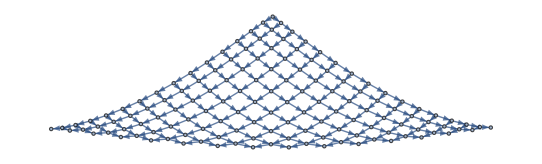

```mathematica
NetSummary[n·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n,n+1}},{n,1,15}]]
FromReducedNetDifferenceSets[%]//Short
FromNetDifferenceSets[%]//Short
Graph[%,GraphLayout->"SpringElectricalEmbedding"]
```

One tweak makes it a cone!  Is this 3-D now?  Maybe not, maybe still 2-D.

```mathematica
NetSummary[(n+1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n+1)·{{n,n+1}},{n,1,20}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[(n+1)·{{n,n+1}}]

{2·{{1,2}},3·{{2,3}},4·{{3,4}},5·{{4,5}},6·{{5,6}},7·{{6,7}},8·{{7,8}},9·{{8,9}},10·{{9,10}},11·{{10,11}},12·{{11,12}},13·{{12,13}},14·{{13,14}},15·{{14,15}},16·{{15,16}},17·{{16,17}},18·{{17,18}},19·{{18,19}},20·{{19,20}},21·{{20,21}}}

-Graphics3D-

Having 3 connections from each node apparently does not equate to 3-D:

```mathematica
NetSummary[n·{{n,n+1,n+2}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n,n+1,n+2}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[n·{{n,n+1,n+2}}]

{1·{{1,2,3}},2·{{2,3,4}},3·{{3,4,5}},4·{{4,5,6}},5·{{5,6,7}},6·{{6,7,8}},7·{{7,8,9}},8·{{8,9,10}},9·{{9,10,11}},10·{{10,11,12}}}

-Graphics3D-

An interesting hybrid:

```mathematica
NetSummary[n·{{n,n+2}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n,n+2}},{n,1,25}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[n·{{n,n+2}}]

{1·{{1,3}},2·{{2,4}},3·{{3,5}},4·{{4,6}},5·{{5,7}},6·{{6,8}},7·{{7,9}},8·{{8,10}},9·{{9,11}},10·{{10,12}},11·{{11,13}},12·{{12,14}},13·{{13,15}},14·{{14,16}},15·{{15,17}},16·{{16,18}},17·{{17,19}},18·{{18,20}},19·{{19,21}},20·{{20,22}},21·{{21,23}},22·{{22,24}},23·{{23,25}},24·{{24,26}},25·{{25,27}}}

-Graphics3D-

Try a fixed number of copies:  still 2-D?!

𝕊_(n=1)^∞[2·{{n,n+1}}]

{2·{{1,2}},2·{{2,3}},2·{{3,4}},2·{{4,5}},2·{{5,6}},2·{{6,7}},2·{{7,8}},2·{{8,9}},2·{{9,10}},2·{{10,11}},2·{{11,12}},2·{{12,13}},2·{{13,14}},2·{{14,15}},2·{{15,16}},2·{{16,17}},2·{{17,18}},2·{{18,19}},«14»,2·{{33,34}},2·{{34,35}},2·{{35,36}},2·{{36,37}},2·{{37,38}},2·{{38,39}},2·{{39,40}},2·{{40,41}},2·{{41,42}},2·{{42,43}},2·{{43,44}},2·{{44,45}},2·{{45,46}},2·{{46,47}},2·{{47,48}},2·{{48,49}},2·{{49,50}},2·{{50,51}}}

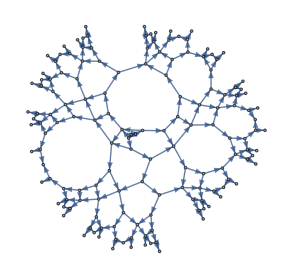

```mathematica
NetSummary[2·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[2·{{n,n+1}},{n,1,50}]]//Short[#,8]&
Graph@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

```mathematica
NetSummary[3·{{n,n+1}},{n,2,∞}]
ExpandAll[NetSummary[3·{{n,n+1}},{n,2,50}]]//Short
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=2)^∞[3·{{n,n+1}}]

{3·{{2,3}},3·{{3,4}},3·{{4,5}},«44»,3·{{49,50}},3·{{50,51}}}

-Graphics3D-

Does n^2·{n...} make it 3-D?  It doesn’t look like it:

```mathematica
NetSummary[n^2·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[n^2·{{n,n+1}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[n^2·{{n,1+n}}]

{1·{{1,2}},4·{{2,3}},9·{{3,4}},16·{{4,5}},25·{{5,6}},36·{{6,7}},49·{{7,8}},64·{{8,9}},81·{{9,10}},100·{{10,11}}}

-Graphics3D-

(n-1)·{n...} spirals the opposite direction from (n+1)·{n...}:

```mathematica
NetSummary[(n-1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n-1)·{{n,n+1}},{n,1,50}]]//Short
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^∞[(n-1)·{{n,n+1}}]

{0·{{1,2}},1·{{2,3}},2·{{3,4}},«45»,48·{{49,50}},49·{{50,51}}}

-Graphics3D-

Even though the following only has 1 connection (or none!) per graph vertex, it should be considered 2-D:  line up the increasingly long line segments in a row, one direction takes you to the next segment, but the second dimension appears in the increasing lengths.

𝕊_(n=1)^∞[n·{{n}}]

{1·{{1}},2·{{2}},3·{{3}},4·{{4}},5·{{5}},6·{{6}},7·{{7}},8·{{8}},9·{{9}},10·{{10}}}

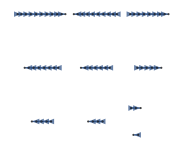

```mathematica
NetSummary[n·{{n}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n}},{n,1,10}]]
Graph[FromNetDifferenceSets@FromReducedNetDifferenceSets@%,GraphLayout->{PackingLayout->"NestedGrid"}]
```

And no, 4 connections doesn’t mean 4-D:

```mathematica
NetSummary[n·{{n,n+1,n+2,n+3}},{n,1,5}]
ExpandAll[NetSummary[n·{{n,n+1,n+2,n+3}},{n,1,10}]]
Graph3D@FromNetDifferenceSets@FromReducedNetDifferenceSets@%
```

𝕊_(n=1)^5[n·{{n,n+1,n+2,n+3}}]

{1·{{1,2,3,4}},2·{{2,3,4,5}},3·{{3,4,5,6}},4·{{4,5,6,7}},5·{{5,6,7,8}},6·{{6,7,8,9}},7·{{7,8,9,10}},8·{{8,9,10,11}},9·{{9,10,11,12}},10·{{10,11,12,13}}}

-Graphics3D-

### Try finding the dimension algorithmically....

𝕊_(n=1)^∞[n·{{n^2,1+n^2}}]

{1·{{1,2}},2·{{4,5}},3·{{9,10}},4·{{16,17}},5·{{25,26}},6·{{36,37}},7·{{49,50}},8·{{64,65}},9·{{81,82}},10·{{100,101}},11·{{121,122}},12·{{144,145}},13·{{169,170}},14·{{196,197}},15·{{225,226}},16·{{256,257}},17·{{289,290}},18·{{324,325}},19·{{361,362}},20·{{400,401}}}

{{1,2},{4,5},{4,5},{9,10},{9,10},{9,10},{16,17},{16,17},{16,17},{16,17},{25,26},{25,26},{25,26},{25,26},{25,26},{36,37},{36,37},{36,37},{36,37},{36,37},{36,37},{49,50},{49,50},{49,50},{49,50},{49,50},{49,50},{49,50},{64,65},{64,65},{64,65},{64,65},{64,65},{64,65},{64,65},{64,65},{81,82},{81,82},{81,82},{81,82},{81,82},{81,82},{81,82},{81,82},{81,82},{100,101},{100,101},{100,101},{100,101},{100,101},{100,101},{100,101},{100,101},{100,101},{100,101},{121,122},{121,122},{121,122},{121,122},{121,122},{121,122},{121,122},{121,122},{121,122},{121,122},{121,122},{144,145},{144,145},{144,145},{144,145},{144,145},{144,145},{144,145},{144,145},{144,145},{144,145},{144,145},{144,145},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{169,170},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{196,197},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{225,226},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{256,257},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{289,290},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{324,325},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{361,362},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401},{400,401}}

{1→2,1→3,2→6,2→7,3→7,3→8,4→13,4→14,5→14,5→15,6→15,6→16,7→23,7→24,8→24,8→25,9→25,9→26,10→26,10→27,11→36,11→37,12→37,12→38,13→38,13→39,14→39,14→40,15→40,15→41,16→52,16→53,17→53,17→54,18→54,18→55,19→55,19→56,20→56,20→57,21→57,21→58,22→71,22→72,23→72,23→73,24→73,24→74,25→74,25→75,26→75,26→76,27→76,27→77,28→77,28→78,29→93,29→94,30→94,30→95,31→95,31→96,32→96,32→97,33→97,33→98,34→98,34→99,35→99,35→100,36→100,36→101,37→118,37→119,38→119,38→120,39→120,39→121,40→121,40→122,41→122,41→123,42→123,42→124,43→124,43→125,44→125,44→126,45→126,45→127,46→146,46→147,47→147,47→148,48→148,48→149,49→149,49→150,50→150,50→151,51→151,51→152,52→152,52→153,53→153,53→154,54→154,54→155,55→155,55→156,56→177,56→178,57→178,57→179,58→179,58→180,59→180,59→181,60→181,60→182,61→182,61→183,62→183,62→184,63→184,63→185,64→185,64→186,65→186,65→187,66→187,66→188,67→211,67→212,68→212,68→213,69→213,69→214,70→214,70→215,71→215,71→216,72→216,72→217,73→217,73→218,74→218,74→219,75→219,75→220,76→220,76→221,77→221,77→222,78→222,78→223,79→248,79→249,80→249,80→250,81→250,81→251,82→251,82→252,83→252,83→253,84→253,84→254,85→254,85→255,86→255,86→256,87→256,87→257,88→257,88→258,89→258,89→259,90→259,90→260,91→260,91→261,92→288,92→289,93→289,93→290,94→290,94→291,95→291,95→292,96→292,96→293,97→293,97→294,98→294,98→295,99→295,99→296,100→296,100→297,101→297,101→298,102→298,102→299,103→299,103→300,104→300,104→301,105→301,105→302,106→331,106→332,107→332,107→333,108→333,108→334,109→334,109→335,110→335,110→336,111→336,111→337,112→337,112→338,113→338,113→339,114→339,114→340,115→340,115→341,116→341,116→342,117→342,117→343,118→343,118→344,119→344,119→345,120→345,120→346,121→377,121→378,122→378,122→379,123→379,123→380,124→380,124→381,125→381,125→382,126→382,126→383,127→383,127→384,128→384,128→385,129→385,129→386,130→386,130→387,131→387,131→388,132→388,132→389,133→389,133→390,134→390,134→391,135→391,135→392,136→392,136→393,137→426,137→427,138→427,138→428,139→428,139→429,140→429,140→430,141→430,141→431,142→431,142→432,143→432,143→433,144→433,144→434,145→434,145→435,146→435,146→436,147→436,147→437,148→437,148→438,149→438,149→439,150→439,150→440,151→440,151→441,152→441,152→442,153→442,153→443,154→478,154→479,155→479,155→480,156→480,156→481,157→481,157→482,158→482,158→483,159→483,159→484,160→484,160→485,161→485,161→486,162→486,162→487,163→487,163→488,164→488,164→489,165→489,165→490,166→490,166→491,167→491,167→492,168→492,168→493,169→493,169→494,170→494,170→495,171→495,171→496,172→533,172→534,173→534,173→535,174→535,174→536,175→536,175→537,176→537,176→538,177→538,177→539,178→539,178→540,179→540,179→541,180→541,180→542,181→542,181→543,182→543,182→544,183→544,183→545,184→545,184→546,185→546,185→547,186→547,186→548,187→548,187→549,188→549,188→550,189→550,189→551,190→551,190→552,191→591,191→592,192→592,192→593,193→593,193→594,194→594,194→595,195→595,195→596,196→596,196→597,197→597,197→598,198→598,198→599,199→599,199→600,200→600,200→601,201→601,201→602,202→602,202→603,203→603,203→604,204→604,204→605,205→605,205→606,206→606,206→607,207→607,207→608,208→608,208→609,209→609,209→610,210→610,210→611}

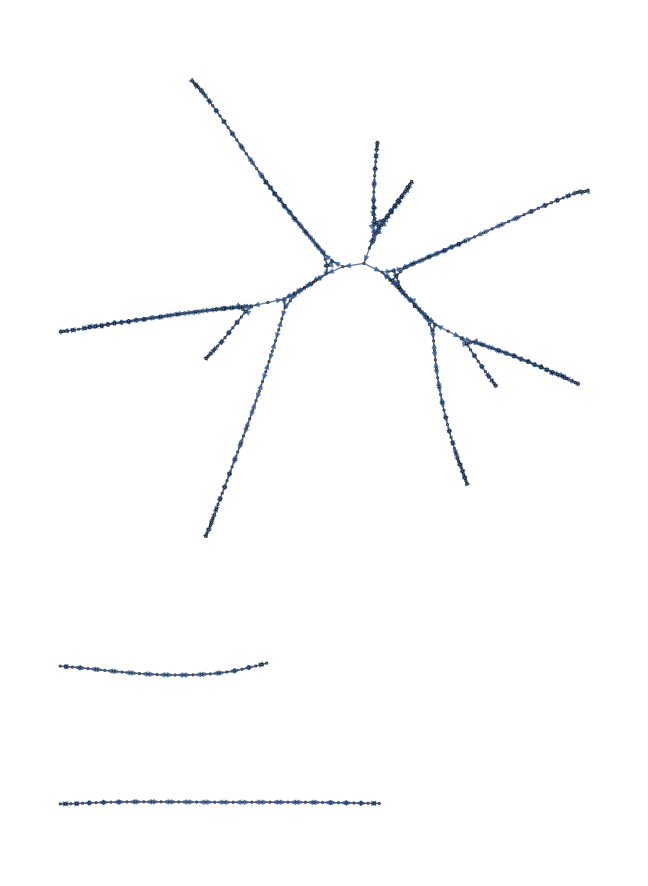

```mathematica
NetSummary[n·{{n^2,n^2+1}},{n,1,∞}]
ExpandAll[NetSummary[n·{{n^2,n^2+1}},{n,1,20}]]
FromReducedNetDifferenceSets@%
FromNetDifferenceSets@%
Graph[%]
```

```mathematica
Graph3D[%60]
```

-Graphics3D-

```mathematica
NetSummary[(n-1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n-1)·{{n,n+1}},{n,1,20}]]
FromReducedNetDifferenceSets@%
FromNetDifferenceSets@%
Graph3D[%]
```

𝕊_(n=1)^∞[(n-1)·{{n,n+1}}]

{0·{{1,2}},1·{{2,3}},2·{{3,4}},3·{{4,5}},4·{{5,6}},5·{{6,7}},6·{{7,8}},7·{{8,9}},8·{{9,10}},9·{{10,11}},10·{{11,12}},11·{{12,13}},12·{{13,14}},13·{{14,15}},14·{{15,16}},15·{{16,17}},16·{{17,18}},17·{{18,19}},18·{{19,20}},19·{{20,21}}}

{{2,3},{3,4},{3,4},{4,5},{4,5},{4,5},{5,6},{5,6},{5,6},{5,6},{6,7},{6,7},{6,7},{6,7},{6,7},{7,8},{7,8},{7,8},{7,8},{7,8},{7,8},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{8,9},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{9,10},{10,11},{10,11},{10,11},{10,11},{10,11},{10,11},{10,11},{10,11},{10,11},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{11,12},{12,13},{12,13},{12,13},{12,13},{12,13},{12,13},{12,13},{12,13},{12,13},{12,13},{12,13},{13,14},{13,14},{13,14},{13,14},{13,14},{13,14},{13,14},{13,14},{13,14},{13,14},{13,14},{13,14},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{14,15},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{15,16},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{16,17},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{17,18},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{18,19},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{19,20},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21},{20,21}}

{1→3,1→4,2→5,2→6,3→6,3→7,4→8,4→9,5→9,5→10,6→10,6→11,7→12,7→13,8→13,8→14,9→14,9→15,10→15,10→16,11→17,11→18,12→18,12→19,13→19,13→20,14→20,14→21,15→21,15→22,16→23,16→24,17→24,17→25,18→25,18→26,19→26,19→27,20→27,20→28,21→28,21→29,22→30,22→31,23→31,23→32,24→32,24→33,25→33,25→34,26→34,26→35,27→35,27→36,28→36,28→37,29→38,29→39,30→39,30→40,31→40,31→41,32→41,32→42,33→42,33→43,34→43,34→44,35→44,35→45,36→45,36→46,37→47,37→48,38→48,38→49,39→49,39→50,40→50,40→51,41→51,41→52,42→52,42→53,43→53,43→54,44→54,44→55,45→55,45→56,46→57,46→58,47→58,47→59,48→59,48→60,49→60,49→61,50→61,50→62,51→62,51→63,52→63,52→64,53→64,53→65,54→65,54→66,55→66,55→67,56→68,56→69,57→69,57→70,58→70,58→71,59→71,59→72,60→72,60→73,61→73,61→74,62→74,62→75,63→75,63→76,64→76,64→77,65→77,65→78,66→78,66→79,67→80,67→81,68→81,68→82,69→82,69→83,70→83,70→84,71→84,71→85,72→85,72→86,73→86,73→87,74→87,74→88,75→88,75→89,76→89,76→90,77→90,77→91,78→91,78→92,79→93,79→94,80→94,80→95,81→95,81→96,82→96,82→97,83→97,83→98,84→98,84→99,85→99,85→100,86→100,86→101,87→101,87→102,88→102,88→103,89→103,89→104,90→104,90→105,91→105,91→106,92→107,92→108,93→108,93→109,94→109,94→110,95→110,95→111,96→111,96→112,97→112,97→113,98→113,98→114,99→114,99→115,100→115,100→116,101→116,101→117,102→117,102→118,103→118,103→119,104→119,104→120,105→120,105→121,106→122,106→123,107→123,107→124,108→124,108→125,109→125,109→126,110→126,110→127,111→127,111→128,112→128,112→129,113→129,113→130,114→130,114→131,115→131,115→132,116→132,116→133,117→133,117→134,118→134,118→135,119→135,119→136,120→136,120→137,121→138,121→139,122→139,122→140,123→140,123→141,124→141,124→142,125→142,125→143,126→143,126→144,127→144,127→145,128→145,128→146,129→146,129→147,130→147,130→148,131→148,131→149,132→149,132→150,133→150,133→151,134→151,134→152,135→152,135→153,136→153,136→154,137→155,137→156,138→156,138→157,139→157,139→158,140→158,140→159,141→159,141→160,142→160,142→161,143→161,143→162,144→162,144→163,145→163,145→164,146→164,146→165,147→165,147→166,148→166,148→167,149→167,149→168,150→168,150→169,151→169,151→170,152→170,152→171,153→171,153→172,154→173,154→174,155→174,155→175,156→175,156→176,157→176,157→177,158→177,158→178,159→178,159→179,160→179,160→180,161→180,161→181,162→181,162→182,163→182,163→183,164→183,164→184,165→184,165→185,166→185,166→186,167→186,167→187,168→187,168→188,169→188,169→189,170→189,170→190,171→190,171→191,172→192,172→193,173→193,173→194,174→194,174→195,175→195,175→196,176→196,176→197,177→197,177→198,178→198,178→199,179→199,179→200,180→200,180→201,181→201,181→202,182→202,182→203,183→203,183→204,184→204,184→205,185→205,185→206,186→206,186→207,187→207,187→208,188→208,188→209,189→209,189→210,190→210,190→211}

-Graphics3D-

```mathematica
NetSummary[(n-1)·{{n,n+1}},{n,1,∞}]
ExpandAll[NetSummary[(n-1)·{{n,n+1}},{n,1,1000}]]//Short
Graph3D[g1=FromNetDifferenceSets@FromReducedNetDifferenceSets@%];
```

𝕊_(n=1)^∞[(-1+n)·{{n,1+n}}]

{0·{{1,2}},1·{{2,3}},«996»,998·{{999,1000}},999·{{1000,1001}}}

```mathematica
GraphDistance[g1,1]//Short[#,10]&
```

$Aborted

```mathematica
Tally[%]
```

{{0,1},{1,2},{∞,2},{2,4},{3,6},{4,7},{5,9},{6,10},{7,11},{8,12},{9,13},{10,14},{11,15},{12,17},{13,18},{14,19},{15,20},{16,21},{17,22},{18,23},{19,24},{20,25},{21,26},{22,27},{23,28},{24,29},{25,30},{26,31},{27,33},{28,34},{29,35},{30,36},{31,37},{32,38},{33,39},{34,40},{35,41},{36,42},{37,43},{38,44},{39,45},{40,46},{41,47},{42,48},{43,49},{44,50},{45,51},{46,52},{47,53},{48,54},{49,55},{50,56},{51,57},{52,58},{53,59},{54,60},{55,61},{56,62},{57,63},{58,65},{59,66},{60,67},{61,68},{62,69},{63,70},{64,71},{65,72},{66,73},{67,74},{68,75},{69,76},{70,77},{71,78},{72,79},{73,80},{74,81},{75,82},{76,83},{77,84},{78,85},{79,86},{80,87},{81,88},{82,89},{83,90},{84,91},{85,92},{86,93},{87,94},{88,95},{89,96},{90,97},{91,98},{92,99},{93,100},{94,101},{95,26}}

```mathematica
Prepend[%[[4;;]],%[[2]]]
```

{{1,2},{2,4},{3,6},{4,7},{5,9},{6,10},{7,11},{8,12},{9,13},{10,14},{11,15},{12,17},{13,18},{14,19},{15,20},{16,21},{17,22},{18,23},{19,24},{20,25},{21,26},{22,27},{23,28},{24,29},{25,30},{26,31},{27,33},{28,34},{29,35},{30,36},{31,37},{32,38},{33,39},{34,40},{35,41},{36,42},{37,43},{38,44},{39,45},{40,46},{41,47},{42,48},{43,49},{44,50},{45,51},{46,52},{47,53},{48,54},{49,55},{50,56},{51,57},{52,58},{53,59},{54,60},{55,61},{56,62},{57,63},{58,65},{59,66},{60,67},{61,68},{62,69},{63,70},{64,71},{65,72},{66,73},{67,74},{68,75},{69,76},{70,77},{71,78},{72,79},{73,80},{74,81},{75,82},{76,83},{77,84},{78,85},{79,86},{80,87},{81,88},{82,89},{83,90},{84,91},{85,92},{86,93},{87,94},{88,95},{89,96},{90,97},{91,98},{92,99},{93,100},{94,101},{95,26}}

```mathematica
Last/@%
```

{2,4,6,7,9,10,11,12,13,14,15,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,26}

```mathematica
Differences[%]
```

{2,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,-75}

```mathematica
Tally[%]/. {a_,b_}:>b·{a}
```

{1·{0},2·{1},2·{∞},4·{2},6·{3},7·{4},9·{5},10·{6},11·{7},12·{8},13·{9},14·{10},15·{11},17·{12},18·{13},19·{14},20·{15},21·{16},22·{17},23·{18},24·{19},25·{20},26·{21},27·{22},28·{23},29·{24},30·{25},31·{26},33·{27},34·{28},35·{29},36·{30},37·{31},38·{32},39·{33},40·{34},41·{35},42·{36},43·{37},44·{38},45·{39},46·{40},47·{41},48·{42},49·{43},50·{44},51·{45},52·{46},53·{47},54·{48},55·{49},56·{50},57·{51},58·{52},59·{53},60·{54},61·{55},62·{56},63·{57},65·{58},66·{59},67·{60},68·{61},69·{62},70·{63},71·{64},72·{65},73·{66},74·{67},75·{68},76·{69},77·{70},78·{71},79·{72},80·{73},81·{74},82·{75},83·{76},84·{77},85·{78},86·{79},87·{80},88·{81},89·{82},90·{83},91·{84},92·{85},93·{86},94·{87},95·{88},96·{89},97·{90},98·{91},99·{92},100·{93},101·{94},26·{95}}

```mathematica
Subtract[
%261[[6;;-2]] /. n_·{a_}:>{a,n},
%261[[4;;-4]]/. n_·{a_}:>{a,n}] /. {a_,n_}:>n·{a}
```

{3·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},3·{2},3·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2},2·{2}}

```mathematica
{3·3·{2},5·2·{2},2·3·{2},13·2·{2},2·3·{2},29·2·{2},2·3·{2},(>=36)·2·{2}}
```